```mathematica
S :=16
S
Sc := S/2
```

16

```mathematica
cr:={{0,1},{0,0}}
```

```mathematica
an:= {{0,0},{1,0}}
n=.
```

```mathematica
cr ;
```

```mathematica
an ;
```

```mathematica
id2 := {{-1,0},{0,1}}
```

```mathematica
id := IdentityMatrix[2]
```

```mathematica
c[n_]:=SparseArray[KroneckerProduct@@( Table[id,(n-1)]~Join~{cr}~Join~Table[id2,{Sc-n}])]
cd[n_]:=SparseArray[KroneckerProduct@@(Table[id,(n-1)]~Join~{an}~Join~Table[id2,{Sc-n}])]
```

```mathematica
c[1].cd[1] +cd[1].c[1] ;
```

```mathematica
Do[ψ[n] =  (1/Sqrt[2]) *(c[n] + cd[n]),{n,Sc}]
```

```mathematica
Do[ψ[Sc +n] = ( 1/Sqrt[2]) *(-I*c[n] + I*cd[n]),{n,Sc}]
```

```mathematica
Do[ψ[i1,i2] = ψ[i1].ψ[i2],{i1,S},{i2,S}] //Timing
Do[ψ[i3,i4] = ψ[i3].ψ[i4],{i3,S},{i4,S}]
```

{0.053491,Null}

Hamiltonian q = 2

```mathematica
ψ[1,1] ;
q = 2;
J = 1;
```

```mathematica
Js =RandomVariate[NormalDistribution[0,Sqrt[ (J^2)*  (   (q-1)! /  (S^(q-1))  ) ]],{S,S}]
```

{{-0.0185682,0.0813419,-0.128479,0.239844,0.22736,-0.350823,0.142102,-0.308322,0.284913,0.2914,-0.330952,0.232132,-0.303041,0.42197,-0.0546247,-0.11685},{0.0808133,-0.245592,-0.157307,0.075899,-0.0238774,-0.00834184,0.222065,0.02999,0.168742,-0.217821,0.247966,-0.0850806,0.0980814,-0.213642,0.0754028,0.153616},{0.236621,0.105905,0.377715,-0.121772,-0.472456,0.235731,-0.0367851,0.0559142,0.0905272,-0.261941,0.163565,-0.0805816,-0.170531,-0.316105,-0.191298,0.0300723},{0.0162516,-0.00643119,0.477207,-0.0395425,0.273054,-0.0538415,0.229286,0.0272972,0.246929,-0.16397,0.242679,-0.343837,-0.039801,0.178668,0.0659389,-0.0859803},{-0.181663,0.411483,-0.38823,0.128016,0.354363,0.0219805,0.119375,-0.203528,-0.430089,0.258972,-0.199695,-0.289749,-0.109075,0.446223,0.176359,-0.360282},{-0.164931,0.381811,0.141785,0.310543,-0.0933857,-0.0223687,0.295682,0.224615,0.516219,-0.312496,-0.0762332,-0.156209,0.0677654,-0.396108,-0.153188,0.132668},{0.35028,-0.229309,0.00435406,-0.208909,0.223748,-0.0981613,-0.175216,0.0379475,0.0104412,-0.0414482,0.220603,-0.304237,-0.397266,-0.483425,0.035444,0.15142},{0.0659013,-0.269399,-0.138294,0.206026,0.335549,-0.354037,0.151409,-0.0471368,0.0468704,-0.149032,0.520608,-0.0225646,-0.0697258,0.293352,0.278538,-0.0292264},{0.250068,0.217015,-0.202745,-0.38172,0.21253,-0.617142,0.0309666,-0.223985,-0.0684681,0.0976588,0.508088,-0.478943,-0.0631594,-0.403391,-0.452167,-0.0968736},{-0.625446,0.0413842,-0.232988,0.0789123,0.230316,-0.287653,0.129549,-0.402354,0.0102112,-0.0590402,-0.537105,-0.15263,-0.315799,-0.167862,0.0162314,0.000863623},{0.0946308,-0.155643,-0.156213,-0.0555633,-0.106783,0.302932,-0.16324,-0.596382,0.303915,0.00876554,-0.0384043,0.105449,0.134669,0.0995717,0.570861,-0.29389},{0.093291,-0.336771,0.0547772,0.103397,-0.0980638,-0.108337,-0.0590698,-0.101773,0.444428,0.0419434,-0.120888,-0.285785,-0.0813816,0.0813147,-0.147761,0.597231},{-0.138755,0.165813,-0.144877,-0.156108,-0.114813,-0.0166544,0.104446,-0.215631,-0.064301,-0.0700499,0.00368724,-0.432806,0.285202,0.0704872,0.094447,0.282856},{0.0877155,-0.1285,0.0798081,-0.406225,-0.24075,-0.107971,0.176449,0.170271,-0.267172,-0.13497,0.253713,0.000839945,-0.0834465,-0.222055,0.0799468,0.326504},{0.0338193,-0.21241,0.259281,0.189664,-0.276032,-0.317419,-0.214508,-0.225475,-0.110681,0.110473,-0.00300268,0.0904052,0.265896,-0.152707,0.126262,0.242296},{0.0559251,0.530681,0.386412,-0.139585,0.187521,-0.259078,-0.0626649,0.031829,0.0489958,0.196945,0.0172631,-0.124216,0.0685907,0.319102,-0.21679,0.321049}}

```mathematica
H=Sum[I* Js[[i1,i2]]*ψ[i1,i2],{i1,S},{i2,i1+1,S}]//Normal;
```

```mathematica
iv =H//N//Eigenvalues//Sort
```

{-3.05517,-2.9766,-2.93554,-2.85696,-2.59718,-2.5186,-2.48772,-2.47754,-2.40915,-2.39897,-2.36809,-2.34866,-2.28952,-2.27009,-2.22903,-2.15045,-2.0956,-2.02973,-2.01703,-1.97597,-1.95115,-1.91009,-1.89739,-1.89067,-1.83152,-1.81209,-1.78121,-1.77103,-1.71427,-1.70264,-1.69246,-1.66158,-1.63761,-1.6357,-1.59463,-1.583,-1.55903,-1.52815,-1.51797,-1.51606,-1.44958,-1.4394,-1.40852,-1.38909,-1.32995,-1.32322,-1.31052,-1.26946,-1.25627,-1.24464,-1.20358,-1.19088,-1.1777,-1.17547,-1.14682,-1.13664,-1.12501,-1.09689,-1.07016,-1.06825,-1.05806,-1.05583,-1.02718,-1.00776,-0.991584,-0.977258,-0.950521,-0.948611,-0.931095,-0.929185,-0.888122,-0.871948,-0.852522,-0.821644,-0.811459,-0.809549,-0.754699,-0.743071,-0.732886,-0.71747,-0.702008,-0.688822,-0.676126,-0.638897,-0.635063,-0.623435,-0.610249,-0.608018,-0.597834,-0.569186,-0.55649,-0.549761,-0.529445,-0.519261,-0.490613,-0.488382,-0.471188,-0.468957,-0.440309,-0.430125,-0.409809,-0.390384,-0.363646,-0.361736,-0.351552,-0.349321,-0.320673,-0.296702,-0.285073,-0.270748,-0.24401,-0.2421,-0.218129,-0.215898,-0.18725,-0.177065,-0.165437,-0.150021,-0.137325,-0.108677,-0.0984925,-0.0962614,-0.0714477,-0.0676138,-0.0481884,-0.0303845,-0.0176885,-0.0109591,0.0109591,0.0176885,0.0303845,0.0481884,0.0676138,0.0714477,0.0962614,0.0984925,0.108677,0.137325,0.150021,0.165437,0.177065,0.18725,0.215898,0.218129,0.2421,0.24401,0.270748,0.285073,0.296702,0.320673,0.349321,0.351552,0.361736,0.363646,0.390384,0.409809,0.430125,0.440309,0.468957,0.471188,0.488382,0.490613,0.519261,0.529445,0.549761,0.55649,0.569186,0.597834,0.608018,0.610249,0.623435,0.635063,0.638897,0.676126,0.688822,0.702008,0.71747,0.732886,0.743071,0.754699,0.809549,0.811459,0.821644,0.852522,0.871948,0.888122,0.929185,0.931095,0.948611,0.950521,0.977258,0.991584,1.00776,1.02718,1.05583,1.05806,1.06825,1.07016,1.09689,1.12501,1.13664,1.14682,1.17547,1.1777,1.19088,1.20358,1.24464,1.25627,1.26946,1.31052,1.32322,1.32995,1.38909,1.40852,1.4394,1.44958,1.51606,1.51797,1.52815,1.55903,1.583,1.59463,1.6357,1.63761,1.66158,1.69246,1.70264,1.71427,1.77103,1.78121,1.81209,1.83152,1.89067,1.89739,1.91009,1.95115,1.97597,2.01703,2.02973,2.0956,2.15045,2.22903,2.27009,2.28952,2.34866,2.36809,2.39897,2.40915,2.47754,2.48772,2.5186,2.59718,2.85696,2.93554,2.9766,3.05517}

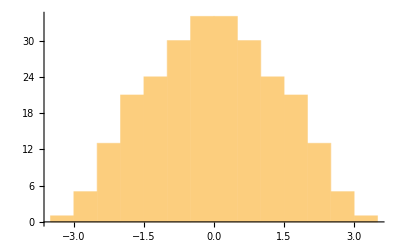

```mathematica
Histogram[iv]
```

```mathematica
q=4
```

4

```mathematica
J=4
```

4

```mathematica
Jm =RandomVariate[NormalDistribution[0,Sqrt[J^2   * ((q-1)!)/(S^(q-1))]],{S,S,S,S}]
```

```mathematica
Dynamic[{i1,i2,i3,i4}]
Ham=I^(q/2)Sum[ψ[i1,i2].Sum[ Jm[[i1,i2,i3,i4]]*ψ[i3,i4],{i3,i2+1,S},{i4,i3 + 1, S}],{i1,S-3},{i2,i1 + 1, S-2}]//Normal;
```

```mathematica
Ham
```

```mathematica
ivv = Ham//N//Eigenvalues//Sort
```

{-3.15393,-3.10652,-3.0479,-2.99596,-2.9619,-2.90983,-2.88907,-2.85597,-2.83771,-2.79765,-2.7592,-2.7325,-2.66624,-2.64938,-2.63757,-2.58452,-2.54662,-2.53809,-2.4864,-2.47722,-2.45806,-2.40174,-2.40091,-2.39696,-2.3476,-2.33248,-2.30413,-2.2998,-2.237,-2.21424,-2.20566,-2.16525,-2.16022,-2.15001,-2.13686,-2.10835,-2.07174,-2.07011,-2.02819,-1.99636,-1.9819,-1.96635,-1.93566,-1.90608,-1.86856,-1.83295,-1.83083,-1.76654,-1.74765,-1.72318,-1.68069,-1.67145,-1.66507,-1.60885,-1.59112,-1.59036,-1.58563,-1.54043,-1.5339,-1.5203,-1.46005,-1.44449,-1.43012,-1.40947,-1.38927,-1.37589,-1.33459,-1.313,-1.30723,-1.27889,-1.27835,-1.21323,-1.20925,-1.1842,-1.17864,-1.14112,-1.13992,-1.11236,-1.07642,-1.0609,-1.03818,-1.03186,-1.01814,-0.97022,-0.939554,-0.92913,-0.912727,-0.892758,-0.880791,-0.845951,-0.829454,-0.785145,-0.772021,-0.73443,-0.725273,-0.709269,-0.680567,-0.680066,-0.659687,-0.632653,-0.621802,-0.611461,-0.556774,-0.515769,-0.513991,-0.497525,-0.474301,-0.443479,-0.432598,-0.425838,-0.387259,-0.349854,-0.343473,-0.335219,-0.331848,-0.244577,-0.227843,-0.226612,-0.21333,-0.205906,-0.157875,-0.144502,-0.125099,-0.112903,-0.0921272,-0.0902872,-0.0433065,-0.0365145,-0.0179059,0.0083685,0.030427,0.0492902,0.0722906,0.133836,0.1387,0.169526,0.176701,0.189919,0.210435,0.220032,0.248892,0.257996,0.304276,0.327352,0.335847,0.342508,0.370833,0.422849,0.424439,0.431497,0.452227,0.46055,0.474033,0.49051,0.525461,0.547257,0.552287,0.562874,0.563939,0.586495,0.633622,0.667828,0.680381,0.695521,0.737431,0.753339,0.766574,0.802023,0.829939,0.834095,0.860952,0.872262,0.932428,0.94378,0.986731,1.02014,1.03677,1.05433,1.07567,1.11305,1.14929,1.1532,1.16792,1.17628,1.21135,1.2427,1.2557,1.26103,1.2792,1.31786,1.36856,1.37047,1.38766,1.414,1.45214,1.48494,1.49536,1.50391,1.52899,1.57661,1.58133,1.60463,1.60685,1.65688,1.67952,1.68596,1.69569,1.7572,1.77677,1.80961,1.8498,1.87178,1.91575,1.91888,1.93244,1.97612,2.02571,2.05472,2.06365,2.08523,2.10933,2.1188,2.14928,2.15977,2.19041,2.2376,2.26396,2.27301,2.28944,2.32166,2.36923,2.39878,2.41619,2.41792,2.4848,2.51164,2.52082,2.54365,2.58173,2.61074,2.67386,2.68102,2.73962,2.81295,2.85661,2.86482,2.9252,2.95324,2.97501,3.00078,3.09907,3.14445,3.18392,3.2358,3.29155,3.32172}

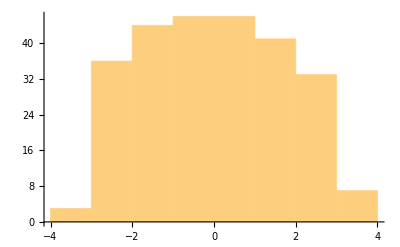

```mathematica
ivv //Histogram
```

Two Point functions

```mathematica
β =5;
H = Ham //N
```

```mathematica
Clear[Gn];
Gn[a_,b_,τ_,β_, λ_]:=Gn[a,b,τ,β ,λ]= Block[{ },
If[τ>0,
Eτ = MatrixExp[-τ H  λ ];
Eβτ = MatrixExp[(-β + τ) H λ];
(Tr[Eβτ.ψ[a].Eτ.ψ[b]]) / (Tr[Eβτ.Eτ]),

Eτ = MatrixExp[+τ H λ];
Eβτ = MatrixExp[(-β - τ) H λ];
-(Tr[Eβτ.ψ[b].Eτ.ψ[a]]) / (Tr[Eβτ.Eτ]),
]
]
```

```mathematica
Gn[1,1,1/4,1,1]
```

0.409132-1.53934×10^-18 ⅈ

```mathematica
Dynamic[tt]
Gn[1,1,1,1,1]
```

0.5+5.77779×10^-34 ⅈ

```mathematica
tbGG =Table[{tt,Gn[1,1,tt,1,1]},{tt,-1/2,1/2,1/10}]//Re
```

{{-1/2,-0.383696},{-2/5,-0.38762},{-3/10,-0.399723},{-1/5,-0.421034},{-1/10,-0.453445},{0,-0.5},{1/10,0.453445},{1/5,0.421034},{3/10,0.399723},{2/5,0.38762},{1/2,0.383696}}

```mathematica
plt = ListPlot[tbGG,Joined->True]
```

-Graphics-

```mathematica
Spec[τ_,β_]:=Spec[τ,β ]= Block[{ },
If[τ>0,
Zβτm = Tr[MatrixExp[(-β * H)-(I*H*τ)]];
Zβτp = Tr[MatrixExp[(-β * H)+(I*H*τ)]];
Zβ = Tr[MatrixExp[(-β * H )]];
Abs[((Zβτm  *Zβτp )/(Zβ )^2)]
]
]
```

```mathematica
Spec[3,1]
```

0.0591718

```mathematica
tbSpec =Table[{tt,Spec[tt,10]},{tt,1,100,1}];
```

```mathematica
tap=Table[{i,Sum[tbSpec[[i]][[2]],{i,1,i}]},{i,1,100,1}];
```

```mathematica
pltSpec = ListPlot[Log[tbSpec],Joined->True]
```

-Graphics-

```mathematica
pltSpec2 = ListPlot[tap,Joined->True]
```

-Graphics-